```mathematica
r2[ψ_]:=ϵ/(γ0 Cos[ψ]^2+(2 α0)/βm Cos[ψ] Sin[ψ]+β0/βm^2 Sin[ψ]^2)
r2'[ψ]
```

-(ϵ ((2 α0 Cos[ψ]^2)/βm+(2 Cos[ψ] Sin[ψ])/βm-(2 (1+α0^2) Cos[ψ] Sin[ψ])/βm-(2 α0 Sin[ψ]^2)/βm))/((((1+α0^2) Cos[ψ]^2)/βm+(2 α0 Cos[ψ] Sin[ψ])/βm+Sin[ψ]^2/βm)^2)

```mathematica
Simplify[-(ϵ ((2 α0 Cos[ψ]^2)/βm+(2 β0 Cos[ψ] Sin[ψ])/βm^2-2 γ0 Cos[ψ] Sin[ψ]-(2 α0 Sin[ψ]^2)/βm))/((γ0 Cos[ψ]^2+(2 α0 Cos[ψ] Sin[ψ])/βm+(β0 Sin[ψ]^2)/βm^2)^2)]
```

(4 α0 βm ϵ (-2 Cos[2 ψ]+α0 Sin[2 ψ]))/((2+α0^2+α0^2 Cos[2 ψ]+2 α0 Sin[2 ψ])^2)

```mathematica
TrigReduce[Cos[(ArcTan[a]+π)/2] Sin[(ArcTan[a]+π)/2]]
```

-1/(α0 √((4+α0^2)/α0^2))

```mathematica
TrigReduce[Cos[(ArcTan[a]+π)/2]^2]
```

(-1+√((4+α0^2)/α0^2))/(2 √((4+α0^2)/α0^2))

```mathematica
TrigReduce[Sin[(ArcTan[a]+π)/2]^2]
```

(1+√((4+α0^2)/α0^2))/(2 √((4+α0^2)/α0^2))

```mathematica
a=(2 α0 βm)/(βm^2 γ0-β0);
γ0=(1+α0^2)/β0;
β0=βm;
(2 √(1+a^2))/(-γ0 βm-2α0 a+β0/βm+(γ0 βm+β0/βm) √(1+a^2))
```

(2 √(1+(4 α0^2 βm^2)/((-βm+(1+α0^2) βm)^2)))/(-α0^2-(4 α0^2 βm)/(-βm+(1+α0^2) βm)+(2+α0^2) √(1+(4 α0^2 βm^2)/((-βm+(1+α0^2) βm)^2)))

```mathematica
Simplify[%]
```

(2 √(1+4/α0^2))/(-4+2 √(1+4/α0^2)+(-1+√(1+4/α0^2)) α0^2)

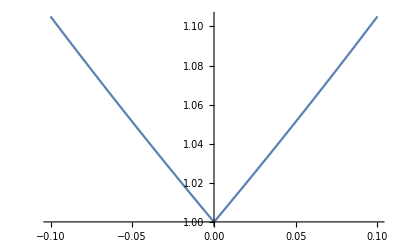

```mathematica
Plot[%,{α0,-0.1,0.1}]
```

```mathematica
f[α0_]=(2 √(α0^2+4))/(-α0^2-4 α0+(α0+2) √(α0^2+4));
Series[f[α0],{α0,0,2}]
```

1+α0/2+α0^2/2+O[α0]^3

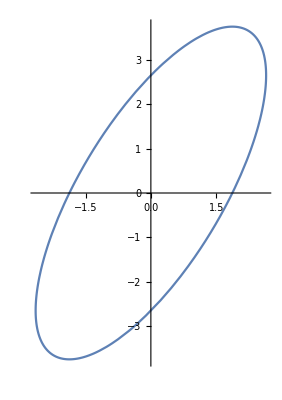

-31.7175

```mathematica
ins={ϵ0->7.,β0->1,βm->1,α0->-1};
r[t_]:=√(ϵ0/(γ0 Cos[t]^2+(2 α0)/βm Cos[t] Sin[t]+β0/βm^2 Sin[t]^2))
PolarPlot[r[t]/.ins,{t,-π,π}]
ψ=N[1/2 ArcTan[(2 α0 βm)/(βm^2 γ0-β0)]/.ins];
ψ 180/π
```

```mathematica
r[ψ+π/2]/.ins
```

4.28092